# On Persistence of Structures in Cellular Automata

## Visualization Code

```mathematica
Clear[ProgressMap]
ProgressMap[f_, l_List]:=Module[{stdout=PrintTemporary[""], len=Length[l], begin=TimeObject[], cur, avg,eta, tmp, cont=True, out, i=0},
out=ConstantArray[0, len];
While[cont,
i++;
out[[i]]=f[l[[i]]];
NotebookDelete[stdout];
cur=TimeObject[];avg=(cur-begin)/i;eta=begin+len*avg;stdout=PrintTemporary["Step "<>ToString[i]<>"/"<>ToString[len]<>" ("<>ToString[N[100*i/len]]<>"% complete, Avg Time "<>ToString[QuantityMagnitude[avg,"Seconds"]]<>" seconds per elem, ETA "<>DateString[eta, "DateTimeShort"]<>") ", Button["Stop", cont=False]]; 
If[i>=len, cont=False];
];
out[[;;i]]
]
ProgressMap[f_, l_Integer]:=ProgressMap[f, ConstantArray[0, l]]
```

```mathematica
RunCA[rule_,init_List,steps_]:=CellularAutomaton[rule,{init,0},steps]
RunCA[rule_,init_Integer,steps_]:=RunCA[rule,IntegerDigits[init,AnalyzeRule[rule]["Colors"]],steps]
```

```mathematica
PointApplyRule[rule_,init_]:=CellularAutomaton[rule,init,1]⟦2,(Length[init]+1)/2⟧
```

```mathematica
AnalyzeRule[{n_,{k_,1},r_}]:=AnalyzeRule[{n,{k,1},r}]=With[{rule={n,{k,1},r}},{num=FromDigits[Reverse[(PointApplyRule[rule,#1]&)/@Tuples[Range[0,k-1],2 r+1]],k]},Join[AnalyzeRule[{num,k,r}],Association["Rule"->rule,"Totalistic"->True]]]

AnalyzeRule[{n_,k_,r_}]:=AnalyzeRule[{n,k,r}]=Module[{rule={n,k,r}},Association["Rule"->rule,"NormalRule"->rule,"Colors"->k,"Radius"->r,"Totalistic"->False,"Number"->n,"Quiescent"->!Positive[PointApplyRule[rule,ConstantArray[0,2 r+1]]],"Symmetric"->AllTrue[Tuples[Range[0,k-1],2 r+1],PointApplyRule[rule,#1]==PointApplyRule[rule,Reverse[#1]]&]]]

AnalyzeRule[{n_,k_}]:=AnalyzeRule[{n,k,1}]
AnalyzeRule[{n_}]:=AnalyzeRule[{n,2}]
AnalyzeRule[n_]:=AnalyzeRule[{n}]
```

```mathematica
AArrayPlot[rule_,init_List,steps_Integer:100,ops:OptionsPattern[ArrayPlot]]:=ArrayPlot[RunCA[rule,init,steps],{ops}]

AArrayPlot[rule_,init_Integer,args___]:=AArrayPlot[rule,IntegerDigits[init,AnalyzeRule[rule]["Colors"]],args]
```

## Abstract

A cellular automaton is an arrangement of cells whose values update based on a set of local rules. A structure in such a system is persistent if and only if it never dies out (all cells become zero), but either repeats or grows forever.

This project explores the behavior of persistent structures in one-dimensional cellular automata, how to efficiently search for such structures, and the possible applications of such systems to other processes including biological growth and evolution.

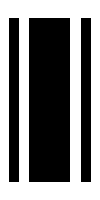
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-Some Classes of Persistent Structure:

```mathematica
Labeled[Row[{
Labeled[AArrayPlot[{20, {2, 1}, 2}, 189, 20, ImageSize->{100, 200}], "Fixed\nPoint", Top], Labeled[AArrayPlot[{114, {3, 1}, 1}, 597871, 50, ImageSize->{100, 200}], "Periodic", Top],
Labeled[AArrayPlot[{100,{2,1},3}, 1399, 60, ImageSize->{100, 200}], "Glider", Top],
Labeled[AArrayPlot[{870,{3,1},1}, 24650, 200, ImageSize->{100, 200}], "Structured Growth", Top],
Labeled[AArrayPlot[{681,{3,1},1}, 70, 100, ImageSize->{100, 200}], "Self-\nSimilar", Top],
Labeled[AArrayPlot[{1521,{3,1},1}, 2, 500, ImageSize->{100, 200}], "Complex Growth", Top]
}, Spacer[1]], Style["Some Classes of Persistent Structure:", Bold], Top, Spacings->{0,1}]
```

```mathematica
Labeled[Row[
AArrayPlot[{20, {2, 1}, 2}, #, 100, ImageSize->{Automatic, 200}]&/@{151,187,189,635,15903,125231,595703,610999,14871103,22503642597,222678959859,10469510870511,360759087837221,2197520782601119}
, Spacer[1]], Style["Search Results for First 100,000,000,000,000 Initial Conditions to Code 20:", Bold], Top, Spacings->{0,1}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-Search Results for First 100,000,000,000,000 Initial Conditions to Code 20:

## Introduction

## Methods

While some better methods exist for finding large periodic structures, only brute force search works to find any general persistent structure. I

## Classification Algorithm

## GPU Search

## Results

## Frequency Analysis

### Persistent Structure Frequency (How many initial conditions are persistent?)

#### Goal

#### Results

This shows the frequency of persistent initial conditions as the initial conditions get larger for the code 20 cellular automata. Most small initial conditions die, but as they get larger, the tend to live more often.

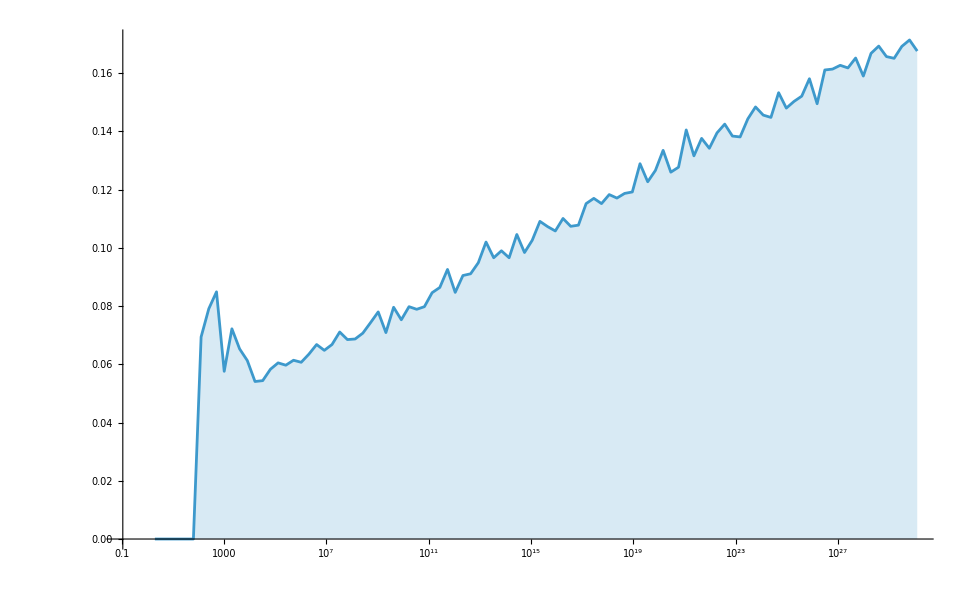

```mathematica
Clear[IsPersistent];
IsPersistent[init_]:=Unitize[Total[CellularAutomaton[{20, {2, 1}, 2},{IntegerDigits[init, 2], 0}, {{{1000}}}]]]

FrequencyOf[func_, min_, max_, n_]:=N[Total[ParallelMap[func, RandomInteger[{min, max}, n]]]]/n

res=ProgressMap[{2^#, FrequencyOf[IsPersistent, 2^#, 2^(#+1), 10000]}&, Range[100]];

ListLogLinearPlot[res, Joined->True,  Filling->Axis]
```

This can be largely explained by the fact that if one init is twice as long as another init, then it is likely to contain about twice as many places where a structure might form, and therefore the probability that it will persist is increased.

Alternatively, here is the same plot for the code 1329 automata, which is much more fruitful in terms of persistent structures:

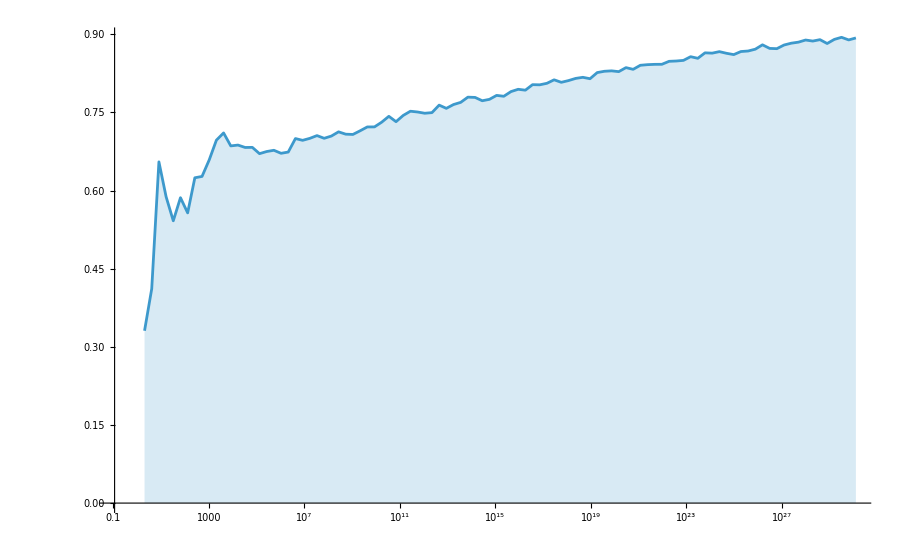

```mathematica
Clear[IsPersistent];
IsPersistent[init_]:=Unitize[Total[CellularAutomaton[{1329, {3, 1}, 1},{IntegerDigits[init, 3], 0}, {{{5000}}}]]]

FrequencyOf[func_, min_, max_, n_]:=N[Total[ParallelMap[func, RandomInteger[{min, max}, n]]]]/n

res=ProgressMap[{2^#, FrequencyOf[IsPersistent, 2^#, 2^(#+1), 10000]}&, Range[100]];

ListLogLinearPlot[res, Joined->True,  Filling->Axis]
```

To better compare how different rules behave, here is the same plot shown for all totalistic quiescent k=2 r=2 rules:

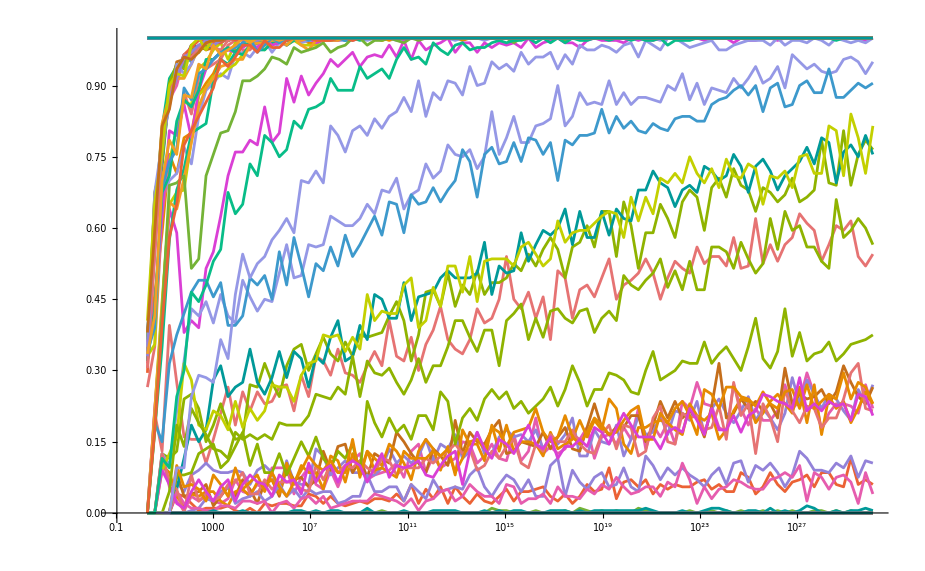

```mathematica
Clear[IsPersistent];
IsPersistent[rule_][init_]:=Unitize[Total[CellularAutomaton[rule,{IntegerDigits[init, 2], 0}, {{{400}}}]]]

FrequencyOf[func_, min_, max_, n_]:=N[Total[Map[func, RandomInteger[{min, max}, n]]]]/n

rules= ;
res=ParallelMap[rule|->Tooltip[Map[{2^#, FrequencyOf[IsPersistent[rule], 2^#, 2^(#+1), 200]}&, Range[100]], rule], rules]

ListLogLinearPlot[res, Joined->True]
```

### Unbounded Growth Frequency (How many initial conditions exhibit unbounded growth?)

For 1329:

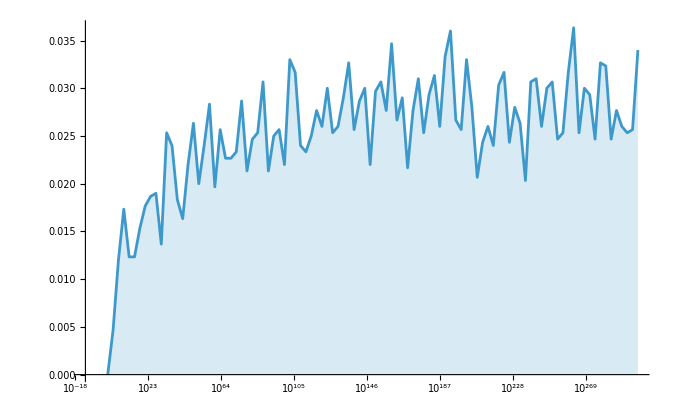

```mathematica
Clear[IsUnbounded];
IsUnbounded[rule_][init_]:=Boole[With[{run=RunCA[rule, init, 5000]}, Max[Last[run]]!=0&&Length[FindRepeatDeterministicByStripZeros[run]]==0]]

FrequencyOf[func_, min_, max_, n_]:=N[Total[ParallelMap[func, RandomInteger[{min, max}, n]]]]/n

res=ProgressMap[{2^#, FrequencyOf[IsUnbounded[{1329, {3, 1}, 1}], 2^#, 2^(#+1), 3000]}&, Range[1,1000, 10]];

ListLogLinearPlot[res, Joined->True,  Filling->Axis]
```

Why is that the case?????

```mathematica
Clear[IsUnbounded];
IsUnbounded[rule_][init_]:=Boole[With[{run=RunCA[rule, init, 2000]}, Max[Last[run]]!=0&&Length[FindRepeatDeterministicByStripZeros[run]]==0]]

Clear[IsPersistent];
IsPersistent[rule_][init_]:=Unitize[Total[CellularAutomaton[rule,{IntegerDigits[init, 2], 0}, {{{1000}}}]]]

FrequencyOf[func_, min_, max_, n_]:=N[Total[ParallelMap[func, RandomInteger[{min, max}, n]]]]/n


res=Transpose[ProgressMap[size|->With[
{rule={1329, {3, 1}, 1}, n=10000},
{min=2^size, max=2^(size+1)},
{
unboundedFreq=FrequencyOf[IsUnbounded[rule],min, max, n],
persistentFreq=FrequencyOf[IsPersistent[rule], min, max, n]
},

{2^size, #}&/@{unboundedFreq, persistentFreq-unboundedFreq, 1-persistentFreq}
], Range[100]]];
```

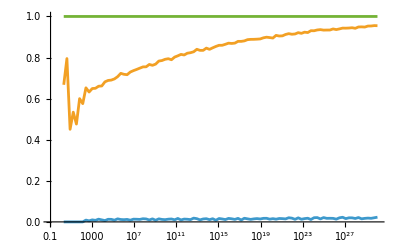

```mathematica
ListLogLinearPlot[res, Joined->True,  PlotLayout->"Stacked"]
```

Detection isn’t perfect, but still pretty good:

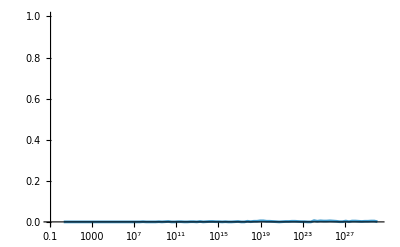

```mathematica
Clear[IsUnbounded];
IsUnbounded[rule_][init_]:=Boole[With[{run=RunCA[rule, init, 200]}, Max[Last[run]]!=0&&Length[FindRepeatDeterministicByStripZeros[run]]==0]]

FrequencyOf[func_, min_, max_, n_]:=N[Total[ParallelMap[func, RandomInteger[{min, max}, n]]]]/n

res=ProgressMap[{2^#, FrequencyOf[IsUnbounded[{20, {2, 1}, 2}], 2^#, 2^(#+1), 1000]}&, Range[100]];

ListLogLinearPlot[res, Joined->True,  Filling->Axis, PlotRange->{Automatic, {0, 1}}]
```

### Periodicity Frequency (What periods are most often seen in repeating structures?)

```mathematica
dataset=ProgressMap[rule|->TimeConstrained[DedupSame[Catenate[ParallelMap[DetectPeriod[rule, #]&,GPUStructureSearch[rule, 0, 1000000][[;;UpTo[1000]]]]]][[All, "Period"]], 60, {}],];
```

$Aborted

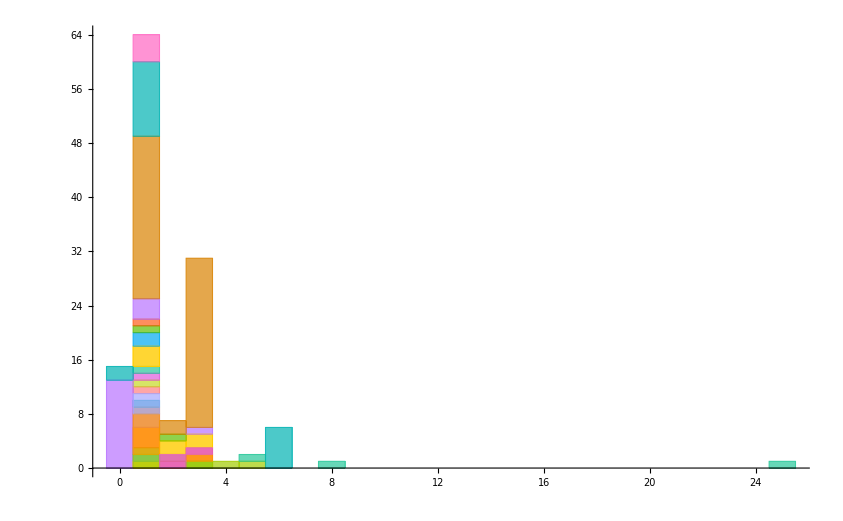

```mathematica
Histogram[dataset, {1}, PlotRange->All, ChartLayout->"Stacked"]
```

$Aborted

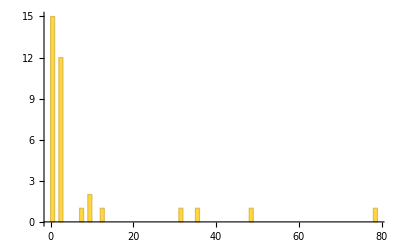

```mathematica
rule={1329,{3, 1},1};
ress=DedupSame[Join@@ParallelMap[DetectPeriod[rule, #]&,GPUStructureSearch[rule, 0, 10000000]]];

Histogram[ress[[All, "Period"]], {1}, PlotRange->All]
```

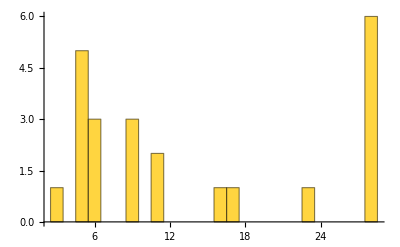

```mathematica
rule={287678469601282591390180274541204957208,2,3};
ress=DedupSame[Join@@ParallelMap[DetectPeriod[rule, #]&,GPUStructureSearch[rule, 0, 100000000]]];

Histogram[ress[[All, "Period"]], {1}, PlotRange->All]
```

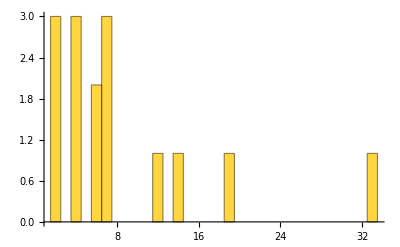

```mathematica
rule={299487394228216260896006481833710814416,2,3};
ress=DedupSame[Join@@ParallelMap[DetectPeriod[rule, #]&,GPUStructureSearch[rule, 0, 100000000]]];

Histogram[ress[[All, "Period"]], {1}, PlotRange->All]
```

```mathematica
rule={287678469601282591390180274541204957208,2,3};
ress=DedupSame[Join@@ParallelMap[DetectPeriod[rule, #]&,GPUStructureSearch[rule, 0, 100000000]]];

Histogram[ress[[All, "Period"]], {1}, PlotRange->All]
```

-Graphics-

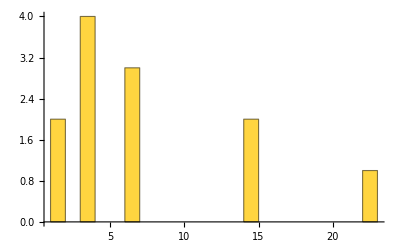

```mathematica
rule={48160796682634112441983828648750880480,2,3};
ress=DedupSame[Join@@ParallelMap[DetectPeriod[rule, #]&,GPUStructureSearch[rule, 0, 100000000]]];

Histogram[ress[[All, "Period"]], {1}, PlotRange->All]
```

### Unique Structure Frequency (How many more steps does it take to find a new structure? )

```mathematica
opencldirectory
```

opencldirectory

```mathematica
NotebookEvaluate[]
```

```mathematica
opencldirectory="/home/chris/Programming/GPU/opencl3/";
```

```mathematica
NotebookEvaluate[opencldirectory<>"DetectPeriodTools2.wl"]
NotebookEvaluate[opencldirectory<>"build.wl"]
```

```mathematica
Clear[ProgressMap]
ProgressMap[f_, l_List]:=Module[{stdout=PrintTemporary[""], len=Length[l], begin=TimeObject[], cur, avg,eta, tmp, cont=True, out, i=0},
out=ConstantArray[0, len];
While[cont,
i++;
out[[i]]=f[l[[i]]];
NotebookDelete[stdout];
cur=TimeObject[];avg=(cur-begin)/i;eta=begin+len*avg;stdout=PrintTemporary["Step "<>ToString[i]<>"/"<>ToString[len]<>" ("<>ToString[N[100*i/len]]<>"% complete, Avg Time "<>ToString[QuantityMagnitude[avg,"Seconds"]]<>" seconds per elem, ETA "<>DateString[eta, "DateTimeShort"]<>") ", Button["Stop", cont=False]]; 
If[i>=len, cont=False];
];
out[[;;i]]
]
ProgressMap[f_, l_Integer]:=ProgressMap[f, ConstantArray[0, l]]
```

#### Code

```mathematica
Clear[PlotDiscoveryFrequency]
PlotDiscoveryFrequency[rule_, max_Integer, dedup_:True, timeout_:120, opts:OptionsPattern[ListLogLinearPlot]]:=TimeConstrained[Module[{},
inits=GPUStructureSearch[rule, 0, max, timeout, True];
inits=inits[[;;UpTo[10000]]];
If[dedup,
ress=DedupSame[SortBy[Join@@ParallelMap[DetectPeriod[rule, #]&, inits], #Original&]];
ress=Sort[ress[[All, "Original"]]];
gliderguns=ParallelMap[AnyTrue[DetectPeriod[rule, #], #IsGliderGun&]&, ress];,

ress=inits;
gliderguns=ConstantArray[False, Length[inits]];
];
resss=Transpose[{ress, Range[Length[ress]]}];

ListLogLinearPlot[
ParallelTable[
With[{all=resss[[i]]},{init=all[[1]]},
Style[
If[dedup||RandomReal[]<20/Length[resss],
Callout[
all,
Tooltip[
ClickToCopy[
AArrayPlot[rule, init,60],
init
],
AArrayPlot[rule, init, 300]
], LabelVisibility->If[dedup,All, Automatic]],
all
],
If[gliderguns[[i]], Red, Blue]
]
],{i, Length[resss]}], 
LabelingSize->{Automatic, 25}, Joined->True, Filling->Axis,InterpolationOrder->0, PlotRange->{{1, max}, All}, opts]

], timeout]
```

#### Analysis

Discovery Frequency plot: 
Initial conditions searched vs number of unique solutions found

Code 20:

```mathematica
EchoTiming@PlotDiscoveryFrequency[{20, {2, 1}, 2}, 10000000000,True, 1000]
```

128.427

-Graphics-

```mathematica
PlotDiscoveryFrequency[{20, {2, 1}, 2}, 1000000000,False, 100,PlotRange->{100, Automatic}]
```

-Graphics-

```mathematica
PlotDiscoveryFrequency[{1329, {3, 1}, 1},  1000000]
```

-Graphics-

```mathematica
PlotDiscoveryFrequency[{1329, {3, 1}, 1},  1000000, False]
```

-Graphics-

```mathematica
PlotDiscoveryFrequency[{1842,{3,1},1},  1000000]
```

-Graphics-

## Conclusion

## Working